{0.409111}

{0.505142}

{0.0632581}

{0.020852}

{0.00136454}

{0.000259151}

{0.0000115159}

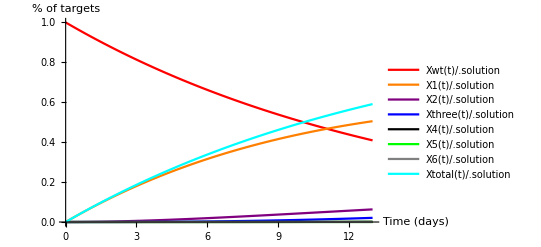

```mathematica
(*This system of ODEs predicts the distribution of editing outcomes at the peCHYRON locus after 13 days of continuous editing, assuming editing efficiencies don't diminish over time.  eta1 = A->B editing efficiency (%/day), eta2 = B->A editing efficiency (%/day), Xwt = fraction of reads with no edits, X1 = fraction of reads with 1 edit, X2 = fraction of reads with 2 edits, and so forth. eta1 and eta2 were calculated as described in the main text.*)

system = {
Xwt'[t] == -eta1*Xwt[t],
X1'[t] == eta1*Xwt[t] - eta2*X1[t],
X2'[t] == eta2*X1[t] - eta1*X2[t],
Xthree'[t] == eta1*X2[t] - eta2*Xthree[t],
X4'[t] == eta2*Xthree[t] - eta1*X4[t],
X5'[t] == eta1*X4[t] - eta2*X5[t],
X6'[t] == eta2*X5[t] - eta1*X6[t],
Xtotal[t] == 1- Xwt[t]};

initials = {Xwt[0]==1,X1[0]==0, X2[0]==0, Xthree[0]==0, X4[0]==0, X5[0]==0, X6[0]==0};
fullsystem = Join[system, initials];

parameters = {eta1 ->0.068751391, eta2 -> 0.021450545}; 
	solution = NDSolve[fullsystem/.parameters, 
{Xwt[t],X1[t], X2[t], Xthree[t], X4[t], X5[t], X6[t], Xtotal[t]},
{t,0,200}];

Xwt[t]/.solution/.t->13
X1[t]/.solution/.t->13
X2[t]/.solution/.t->13
Xthree[t]/.solution/.t->13
X4[t]/.solution/.t->13
X5[t]/.solution/.t->13
X6[t]/.solution/.t->13

Plot[{Xwt[t]/.solution,
X1[t]/.solution,
X2[t]/.solution,
Xthree[t]/.solution,
X4[t]/.solution,
X5[t]/.solution,
X6[t]/.solution,
Xtotal[t]/.solution},
 {t,0,13}, 
PlotRange -> {0, Automatic}, 
PlotStyle ->{{Red, Thick},{Orange,Thick}, {Purple, Thick}, {Blue, Thick}, {Black, Thick}, {Green, Thick}, {Gray,Thick}, {Cyan, Thick}}, 
AxesLabel -> {"Time (days)", "% of targets"}, PlotLegends->"Expressions"]
```